## Mодель Решиньо и Де Лизи роста раковых клеток

Примеры клинических случаев есть в файле с моделью.

-Graphics-

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
x0=2000;
y0=10;
Tmax=100;

ClearAll[x,y,t];
Manipulate[Module[{sol,T=Tmax,x0 = x0,y0 = y0},sol=NDSolve[{x'[t]==-λ1*x[t]+a1*(x[t]*Max[y[t],10^-6]^(2/3)*(1-x[t]/xc))/(1+x[t]),y'[t]==λ2*Max[y[t],10^-6]-a2*(x[t]*Max[y[t],10^-6]^(2/3))/(1+x[t]),x[0]==x0,y[0]==y0},{x,y},{t,0,T}];
Plot[Evaluate[{x[t],y[t]}/. sol],{t,0,T},PlotLabel->StringJoin["Рост количества опухолевых клеток\nλ1 = ",ToString[λ1],", λ2 = ",ToString[λ2],", xc = ",ToString[xc],", a1 = ",ToString[a1],", a2 = ",ToString[a2],", x0 = ", ToString[x0],", y0 = ", ToString[y0]],PlotLegends->{"Лимфоциты","ОК"},PerformanceGoal->"Speed",PlotRange->All]],{λ1,0.01,4,0.01},{λ2,0.1,4,0.01},{xc,50,5000},{a1,0.1,2.8},{a2,0.1,2.8},ContinuousAction->False]
```

NDSolve::nderr: Error test failure at t == 33.2669; unable to continue.

NDSolve::nderr: Error test failure at t == 41.6801; unable to continue.

NDSolve::nderr: Error test failure at t == 48.228; unable to continue.

NDSolve::nderr: Error test failure at t == 89.7351; unable to continue.

NDSolve::nderr: Error test failure at t == 28.3555; unable to continue.

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{x'[t]==-1.61 x[t]+(2.18 Max[«2»]^(2/3) (1+Times[«2»]) x[t])/Plus[«2»],y'[t]==1.78 Max[1/1000000,y[«1»]]-(2.68 Max[«2»]^(2/3) x[t])/Plus[«2»],x[0]==x0,y[0]==y0},{x,y},{t,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000417083 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.000417083]==-1.61 x[0.000417083]+(2.18 Max[«2»]^(2/3) (1+Times[«2»]) x[0.000417083])/Plus[«2»],y'[0.000417083]==1.78 Max[1/1000000,y[«1»]]-(2.68 Max[«2»]^(2/3) x[0.000417083])/Plus[«2»],x[0]==x0,y[0]==y0},{x,y},{0.000417083,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000417083 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.000417083]==-1.61 x[0.000417083]+(2.18 Max[«2»]^(2/3) (1.+Times[«2»]) x[0.000417083])/Plus[«2»],y'[0.000417083]==1.78 Max[1.×10^-6,y[«1»]]-(2.68 Max[«2»]^(2/3) x[0.000417083])/Plus[«2»],x[0.]==x0,y[0.]==y0},{x,y},{0.000417083,0.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.417084 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnl: Endpoint Tmax in {t, 0., Tmax} is not a real number.

ReplaceAll::reps: 
   {NDSolve[{x'[t] == -1.61 x[t] + 
                     1          2/3
         2.18 Max[-------, y[t]]    (1 - 0.0002 x[t]) x[t]
                  1000000
         -------------------------------------------------, 
                             1 + x[t]
                                                      1          2/3
                                          2.68 Max[-------, y[t]]    x[t]
                            1                      1000000
       y'[t] == 1.78 Max[-------, y[t]] - -------------------------------, 
                         1000000                     1 + x[t]
       <<1>>, y[0] == y0}, {<<2>>}, {<<3>>}]} is neither a list of replacement
     rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value Tmax in {t, 0, Tmax}
     is not a machine-sized real number.

NDSolve::ndnl: Endpoint Tmax in {t,0.,Tmax} is not a real number.

ReplaceAll::reps: {NDSolve[{x'[t]==-1.61 x[t]+(2.18 Max[«2»]^(2/3) (1+Times[«2»]) x[t])/Plus[«2»],y'[t]==1.78 Max[1/1000000,y[«1»]]-(2.68 Max[«2»]^(2/3) x[t])/Plus[«2»],x[0]==x0,y[0]==y0},{x,y},{t,0,Tmax}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value Tmax in {t,0,Tmax} is not a machine-sized real number.

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Математическая модель роста опухоли с учетом дихотомии миграции и пролиферации

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
R= 0.1;T = 10;
```

```mathematica
B=0.1;d=0.05;Dn=0.01;Ds=0.1;q=0.2;K=1.5;
k=0.3;Scr=0.7;e=10;Sext=1;
T=100; Tmax = 10;ϵ = 0.01;
```

```mathematica
P1[S_,k_,B_,Scr_,ϵ_]:=k* B*(1-Tanh[ϵ(S-Scr)])/2
```

```mathematica
P2[S_,k_,B_,Scr_,ϵ_]:=k* B*(1-Tanh[ϵ(Scr - S)])/2
```

```mathematica
eqns={D[n1[t,x],t]==B*n1[t,x]-P1[S[t,x],k,B,Scr,ϵ]*n1[t,x]+P2[S[t,x],k,B,Scr,ϵ]*n2[t,x],D[n2[t,x],t]==P1[S[t,x],k,B,Scr,ϵ]*n1[t,x]-P2[S[t,x],k,B,Scr,ϵ]*n2[t,x]-d*n2[t,x]+Dn*D[n2[t,x],x,x],D[m[t,x],t]==d*n2[t,x],D[S[t,x],t]==-q*(K*n1[t,x]+n2[t,x])*(S[t,x]/(S[t,x]+Scr))+Ds*D[S[t,x],x,x]};
```

```mathematica
eqns
```

{n1^(1,0)[t,x]==0.1 n1[t,x]+0.015 n2[t,x] (1-Tanh[0.01 (0.7-S[t,x])])-0.015 n1[t,x] (1-Tanh[0.01 (-0.7+S[t,x])]),n2^(1,0)[t,x]==-0.05 n2[t,x]-0.015 n2[t,x] (1-Tanh[0.01 (0.7-S[t,x])])+0.015 n1[t,x] (1-Tanh[0.01 (-0.7+S[t,x])])+0.01 n2^(0,2)[t,x],m^(1,0)[t,x]==0.05 n2[t,x],S^(1,0)[t,x]==-(0.2 (1.5 n1[t,x]+n2[t,x]) S[t,x])/(0.7+S[t,x])+0.1 S^(0,2)[t,x]}

```mathematica
boundaryConditions={Derivative[0,1][n2][t,0]==0,Derivative[0,1][S][t,0]==0,n1[t,R]==0,n2[t,R]==0,S[t,R]==1};

initialConditions={n1[0,x]==0.2n2[0,x]==0.3,m[0,x]==0.2,S[0,x]==0.2};
```

```mathematica
sol=Quiet@NDSolve[Join[eqns,initialConditions,boundaryConditions],{n1,n2,m,S},{t,0,Tmax},{x,0,R},Method->Automatic];
```

```mathematica
Plot3D[n1[t,r]/. sol,{t,0,Tmax},{r,0,R},PlotLabel->"Динамика делящихся клеток (n1)",AxesLabel->{"Время","Позиция","Плотность"},ColorFunction->"Rainbow"]

Plot3D[n2[t,r]/. sol,{t,0,Tmax},{r,0,R},PlotLabel->"Динамика мигрирующих клеток (n2)",AxesLabel->{"Время","Позиция","Плотность"},ColorFunction->"Rainbow"]

Plot3D[S[t,r]/. sol,{t,0,Tmax},{r,0,R},PlotLabel->"Динамика питательного вещества (S)",AxesLabel->{"Время","Позиция","Концентрация"},ColorFunction->"Rainbow"]
Plot3D[m[t,r]/. sol,{t,0,Tmax},{r,0,R},PlotLabel->"Динамика мертвых клеток",AxesLabel->{"Время","Позиция","Концентрация"},ColorFunction->"Rainbow"]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Manipulate[Module[{sol,ic,bc,eqns,ev},ClearAll["GLobal`*"];eqns ={D[n1[t,x],t]==B*n1[t,x]-P1[S[t,x],k,B,Scr,ϵ]*n1[t,x]+P2[S[t,x],k,B,Scr,ϵ]*n2[t,x],D[n2[t,x],t]==P1[S[t,x],k,B,Scr,ϵ]*n1[t,x]-P2[S[t,x],k,B,Scr,ϵ]*n2[t,x]-d*n2[t,x]+Dn*D[n2[t,x],x,x],
D[m[t,x],t]==d*n2[t,x],D[S[t,x],t]==-q*(Κ*n1[t,x]+n2[t,x])*(S[t,x]/(S[t,x]+Sstar))+Ds*D[S[t,x],x,x]} ;bc ={Derivative[0,1][n2][t,0]==0,Derivative[0,1][S][t,0]==0,n1[t,R]==0,n2[t,R]==0,S[t,R]==1};ic = {n1[0,x]==n1M,n2[0,x]==n2M,m[0,x]==0,S[0,x]==1};
sol = Quiet@NDSolve[Join[eqns,ic,bc],{n1,n2,m,S},{t,0,T},{x,0,R},
Method->Automatic];{Plot3D[n1[t,r]/. sol,{t,0,T},{r,0,R},PlotLabel->"Динамика делящихся клеток (n1)",AxesLabel->{"Время","Позиция","Плотность"},ColorFunction->"Rainbow", (*Угол обзора*)
PlotRange->All,ImageSize->Medium,ViewPoint->Front],Plot3D[n2[t,r]/. sol,{t,0,T},{r,0,R},PlotLabel->"Динамика мигрирующих клеток (n2)",AxesLabel->{"Время","Позиция","Плотность"},ColorFunction->"Rainbow",ViewPoint->Front,PlotRange->Full,ImageSize->Medium],
Plot3D[S[t,r]/. sol,{t,0,T},{r,0,R},PlotLabel->"Динамика питательного вещества (S)",AxesLabel->{"Время","Позиция","Концентрация"},ColorFunction->"Rainbow",PlotRange->Full,ImageSize->Medium,ViewPoint->Front],
Plot3D[m[t,r]/. sol,{t,0,T},{r,0,R},PlotLabel->"Динамика мертвых клеток",AxesLabel->{"Время","Позиция","Плотность"},ColorFunction->"Rainbow",PlotRange->Full,ImageSize->Medium,ViewPoint->Front]}],{B,1,1.24},{Κ,0.001,0.025},{R,0.5},{n1M,10^8},{n2M,10^8},{Scr,0.1,1},{Ds,3*10^-6},{q,4.04,4.16},{Dn,10^-8},{d,0.295,0.305},{T,150},{k,1.2},{ϵ,0.01,1},{Sstar,4.2*10^-3}]
```

NDSolve::dsvar: 0.010725 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{n1^(1,0)[0.010725,x]==1.12 n1[0.010725,x]-n1[0.010725,x] P1[S[«2»],1.2,1.12,0.3,0.958]+n2[0.010725,x] P2[S[«2»],1.2,1.12,0.3,0.958],n2^(1,0)[0.010725,x]==-0.3 n2[0.010725,x]+n1[0.010725,x] P1[S[«2»],1.2,1.12,0.3,0.958]-n2[0.010725,x] P2[S[«2»],1.2,1.12,0.3,0.958]+(n2^(0,2)[0.010725,x])/100000000,m^(1,0)[0.010725,x]==0.3 n2[0.010725,x],«5»,n2^(0,1)[0.010725,0]==0,S^(0,1)[0.010725,0]==0,«3»},{n1,n2,m,S},{«1»},{x,0,0.5},Method→Automatic]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.010725 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{n1^(1,0)[0.010725,x]==1.12 n1[0.010725,x]-1. n1[0.010725,x] P1[S[«2»],1.2,1.12,0.3,0.958]+n2[0.010725,x] P2[S[«2»],1.2,1.12,0.3,0.958],n2^(1,0)[0.010725,x]==-0.3 n2[0.010725,x]+n1[0.010725,x] P1[S[«2»],1.2,1.12,0.3,0.958]-1. n2[0.010725,x] P2[S[«2»],1.2,1.12,0.3,0.958]+1.×10^-8 n2^(0,2)[0.010725,x],m^(1,0)[0.010725,x]==0.3 n2[0.010725,x],«5»,n2^(0,1)[0.010725,0.]==0.,S^(0,1)[0.010725,0.]==0.,«3»},«3»,Method→Automatic]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 10.725 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{n1^(1,0)[10.725,x]==1.12 n1[10.725,x]-n1[10.725,x] P1[S[«2»],1.2,1.12,0.3,0.958]+n2[10.725,x] P2[S[«2»],1.2,1.12,0.3,0.958],n2^(1,0)[10.725,x]==-0.3 n2[10.725,x]+n1[10.725,x] P1[S[«2»],1.2,1.12,0.3,0.958]-n2[10.725,x] P2[S[«2»],1.2,1.12,0.3,0.958]+(n2^(0,2)[10.725,x])/100000000,«7»,S^(0,1)[10.725,0]==0,«3»},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

## модель пролиферативного гомеостаза в нормальной клеточной популяции

```mathematica
d2 = 10.5; 
d3 = 18;
τ4 = 1600;
τ1 = 500000;
τ2 = 500000;
τ3=500000;
h = 0.943;
Lst = 1.2*10^8;
```

```mathematica
ϕ1 = Exp[-d2/τ2]*Exp[-d3/τ3];
ϕ2 = Exp[-d2/τ2];
p12st = (h τ1+(1-h)τ4)/(τ1*((1-h)*(2 ϕ1 -1)τ4-h(τ2(1-ϕ2)+2τ3(ϕ2-ϕ1))));
p14st = p12st*(2ϕ1-1)-1/τ1;
L1st = (h Lst)/(τ4 p14st);
L2st = τ2 p12st L1st(1-ϕ2);
L3st = 2 p12st L1st τ3(ϕ2-ϕ1);
L4st = h Lst;
a = Log[1+p14st/p12st];
b = Log[1/(p12st+p14st)];
p12[t_] := Exp[-a*((L1[t]+L2[t]+L3[t])/((1-h)Lst))^2]*Exp[-b*(L4[t]/(h*Lst))^2];
p14[t_]:= (1-Exp[-a*((L1[t]+L2[t]+L3[t])/((1-h)Lst))^2])Exp[-b*(L4[t]/(h*Lst))^2];
```

В модели описываются 4 стадии жизненного цикла клеток.
L1 -- стадия роста, подготовки к делению
L2 -- стадия покоя, при недостатке зрелых клеток клетки из стадии L2 могут перейти в L3 или L4. Раковые клетки в том числе
L3 -- стадия деления, клетка делится на 2 дочерние, которые переходят в L1.
L4 -- стадия зрелости, клетка обретает специфические функции,но теряет возможность делиться и погибает со временем.
Возможные переходы:
L1 → L2→{ {L3→ L1} || {L4→ death}}

```mathematica
LList = NDSolve[{L1'[t] == 2 p12[t-d2-d3]L1[t-d2-d3]*ϕ1-p12[t]L1[t]-p14[t]L1[t]-L1[t]/τ1,
L2'[t]==-p12[t-d2]L1[t-d2]ϕ2+p12[t]L1[t]-L2[t]/τ2,
L3'[t]== 2 p12[t-d2]L1[t-d2]ϕ2 -2p12[t-d2-d3]L1[t-d2-d3] *ϕ1-L3[t]/τ3,L4'[t]==p14[t]L1[t]-L4[t]/τ4,L1[0]==L1st,L2[0]==L2st,L3[0]==L3st,L4[0]==0.8 L4st},{L1,L2,L3,L4},{t,0,10}]//Flatten
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{L1→InterpolatingFunction[…],L2→InterpolatingFunction[…],L3→InterpolatingFunction[…],L4→InterpolatingFunction[…]}

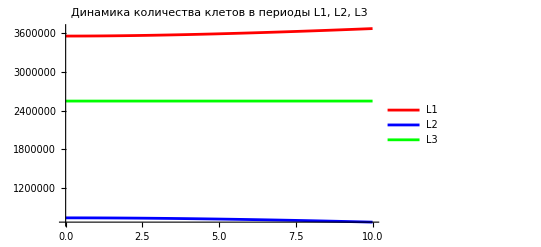

```mathematica
Plot[Evaluate[{L1[t],L2[t],L3[t]}/. LList],{t,0,10},PlotLegends->{"L1","L2","L3","L4"},PlotStyle->{Red,Blue,Green},FrameLabel->{"Time","Value"},PlotLabel->"Динамика количества клетов в периоды L1, L2, L3"]
```

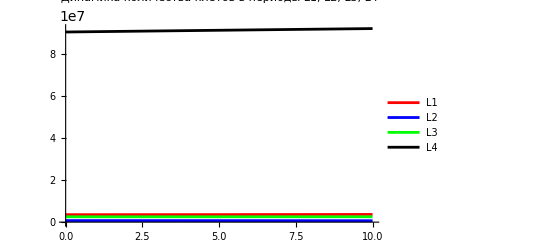

```mathematica
Plot[Evaluate[{L1[t],L2[t],L3[t],L4[t]}/. LList],{t,0,10},PlotLegends->{"L1","L2","L3","L4"},PlotStyle->{Red,Blue,Green,Black},FrameLabel->{"Time","Value"},PlotLabel->"Динамика количества клетов в периоды L1, L2, L3, L4"]
```

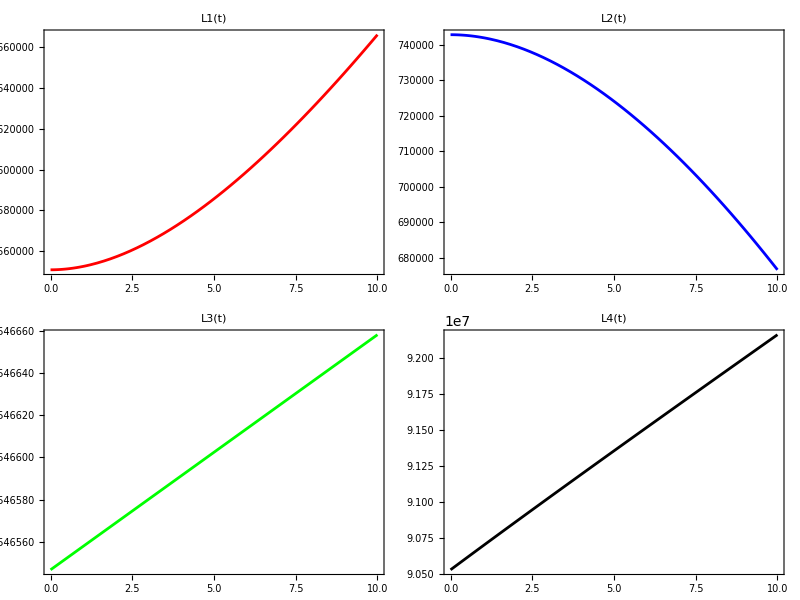

```mathematica
Grid[{{Plot[L1[t]/. LList,{t,0,10},PlotStyle->Red,PlotLabel->"L1(t)",Frame->True,ImageSize->Medium],Plot[L2[t]/. LList,{t,0,10},PlotStyle->Blue,PlotLabel->"L2(t)",Frame->True,ImageSize->Medium]},{Plot[L3[t]/. LList,{t,0,10},PlotStyle->Green,PlotLabel->"L3(t)",Frame->True,ImageSize->Medium],Plot[L4[t]/. LList,{t,0,10},PlotStyle->Black,PlotLabel->"L4(t)",Frame->True,ImageSize->Medium]}}]
```

## НАПРАВЛЕННЫЙ РОСТ И ИНВАЗИЯ ОПУХОЛИ В ОТСУТСТВИИ ХЕМОТАКТИЧЕСКОЙ ПОДВИЖНОСТИ ЕЕ КЛЕТОК

-Graphics-

```mathematica
ClearAll[n,m,h,t,S];
```

```mathematica
B=0.1;       
k=0.5;
ϵ = 0.01;
Sstar=1.0; 
Dn=2.0;
Ds=0.1;
R=400.0;
Tmax=15.0; 
Pm=0.1 ;
Scr = 0.3;
```

```mathematica
P[S_]:= Pm *(1-Tanh[ϵ(S-Scr)])/2;
```

```mathematica
eqns={D[n[t,x,y],t]==B*n[t,x,y]*(1-n[t,x,y])-P[S[t,x,y]]*n[t,x,y]+Div[Dn(1-n[t,x,y])*Grad[n[t,x,y],{x,y}],{x,y}]-Grad[n[t,x,y],{x,y}].Grad[φ[t,x,y],{x,y}] +NeumannValue[0,x==0||y==0],D[m[t,x,y],t]==P[S[t,x,y]]*n[t,x,y]-B*n[t,x,y]*m[t,x,y]-Div[Dn*m[t,x,y]*Grad[n[t,x,y],{x,y}],{x,y}]-Grad[m[t,x,y],{x,y}]*Grad[φ[t,x,y],{x,y}]+NeumannValue[0,x==0||y==0],D[S[t,x,y],t]==-(k*S[t,x,y]*n[t,x,y])/(S[t,x,y]+Sstar)+Ds*Laplacian[S[t,x,y],{x,y}]+NeumannValue[0,x==0||y==0],Laplacian[φ[t,x,y],{x,y}]==B*n[t,x,y]+NeumannValue[0,x==0||y==0]};
```

```mathematica
ic = {n[0,x,y]==10,m[0,x,y]== 0,S[0,x,y]==If[(x==150&&y==400)||(x==400&&y==150),1,0],φ[0,x,y]==0};
```

```mathematica
bc={DirichletCondition[{n[t,x,y]==0,m[t,x,y]==0,S[t,x,y]==0,φ[t,x,y]==0},x==400||y==400]};
```

### роль клеточноЙ подвижности в явлении доминирования МЕТАСТАТИЧЕСКИ АКТИВНЫХ КЛЕТОК В ОПУХОЛИ

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
b1=0.2;   (*Скорость деления клеток субпопуляции 1*)
b2=0.1;  (*Скорость деления клеток субпопуляции 2*)
D1=0.001;  (*Коэффициент диффузии X1*)
D2=10^-8;  (*Коэффициент диффузии X2*)
qs=1.7*10^-5;   (*Скорость потребления субстрата*)
Ss=4.2*10^-6;   (*Константа насыщения субстрата*)
keff=2.0; (*Эффективный коэффициент*)
Ds=3.0*10^-5;   (*Диффузия субстрата*)
Sext=2.8*10^-4; (*Концентрация субстрата на границе*)
R=1;   (*Радиус сферы*)
S0 =0.2;(*2.2*10^-4*)
k = 1.5;(*1.5*)
V = 10^-9;
P1[S_]:=b1*k Exp[-S/Ss];
P2[S_]:=b2*k Exp[-S/Ss];

(*Система уравнений*)
eqns={D[X1[r,t],t]==b1*X1[r,t]-P1[S[r,t]]*X1[r,t]+D1*(D[X1[r,t],r,r]+(2/r)*D[X1[r,t],r])+NeumannValue[0,r==0||r==R],D[Y1[r,t],t]==P1[S[r,t]]*X1[r,t],D[X2[r,t],t]==b2*X2[r,t]-P2[S[r,t]]*X2[r,t]+D2*(D[X2[r,t],r,r]+(2/r)*D[X2[r,t],r])+NeumannValue[0,r==0||r==R],D[Y2[r,t],t]==P2[S[r,t]]*X2[r,t],D[S[r,t],t]==Ds*(D[S[r,t],r,r]+(2/r)*D[S[r,t],r])-(qs*S[r,t]*(X1[r,t]+keff*X2[r,t]))/(Ss+S[r,t])+NeumannValue[0,r==0]};
mesh=ToElementMesh[Line[{{0},{R}}],"IncludePoints"->{{0},{R/2},{R}},(*Контроль точек*)"MaxCellMeasure"->0.01]; (*Точность сетки*)

boundaryConditions={DirichletCondition[S[r,t]==Sext,r==R]};

initialConditions={X1[r,0]==0.05,X2[r,0]==0.05,Y1[r,0]==0.5,Y2[r,0]==0.3,S[r,0]==0.2};

totalCondition=WhenEvent[NIntegrate[V*(X1[r,t]+Y1[r,t]+X2[r,t]+Y2[r,t]),{r,0,R}]>=1,{X1[r,t]->0.99*X1[r,t],X2[r,t]->0.99*X2[r,t],Y1[r,t]->0.99*Y1[r,t],Y2[r,t]->0.99*Y2[r,t]},"Priority"->1];
sol=NDSolve[{eqns,boundaryConditions,initialConditions,totalCondition}//Flatten,{X1,X2,Y1,Y2,S},{r,0,R+0.1},{t,0,1},Method->Automatic]
```

NDSolve::femnlmdor: The maximum derivative order of the nonlinear PDE coefficients for the Finite Element Method is larger than 1. It may help to rewrite the PDE in inactive form.

NDSolve[{X1^(0,1)[r,t]==NeumannValue[0,r==0||r==1]+0.2 X1[r,t]-0.3 ⅇ^(-238095. S[r,t]) X1[r,t]+0.001 ((2 X1^(1,0)[r,t])/r+X1^(2,0)[r,t]),Y1^(0,1)[r,t]==0.3 ⅇ^(-238095. S[r,t]) X1[r,t],X2^(0,1)[r,t]==NeumannValue[0,r==0||r==1]+0.1 X2[r,t]-0.15 ⅇ^(-238095. S[r,t]) X2[r,t]+((2 X2^(1,0)[r,t])/r+X2^(2,0)[r,t])/100000000,Y2^(0,1)[r,t]==0.15 ⅇ^(-238095. S[r,t]) X2[r,t],S^(0,1)[r,t]==NeumannValue[0,r==0]-(0.000017 S[r,t] (X1[r,t]+2. X2[r,t]))/(4.2×10^-6+S[r,t])+0.00003 ((2 S^(1,0)[r,t])/r+S^(2,0)[r,t]),DirichletCondition[S[r,t]==0.00028,r==1],X1[r,0]==0.05,X2[r,0]==0.05,Y1[r,0]==0.5,Y2[r,0]==0.3,S[r,0]==0.2,WhenEvent[NIntegrate[V (X1[r,t]+Y1[r,t]+X2[r,t]+Y2[r,t]),{r,0,R}]≥1,{X1[r,t]→0.99 X1[r,t],X2[r,t]→0.99 X2[r,t],Y1[r,t]→0.99 Y1[r,t],Y2[r,t]→0.99 Y2[r,t]},Priority→1]},{X1,X2,Y1,Y2,S},{r,0,1.1},{t,0,1},Method→Automatic]

## Математическая модель развития рака у пациантов.

```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ = 0.2;
μ1 = 0.004;
μ2 = 0.004;
α = 0.2;
Κ = 0.5;
T0 = 0.025;
γ  = μ1/Κ;
```

```mathematica
sol = NDSolve[{T'[t] == μ1 T[t](1-T[t])-γ T[t] *Ι[t],
Ι'[t]==μ2 Ι[t](1+α T[t]/(T[t]+T0)-Ι[t]/Κ),T[0] == ϵ,Ι[0]==Κ},{T,Ι},{t,0,10}]
```

{{T→InterpolatingFunction[…],Ι→InterpolatingFunction[…]}}

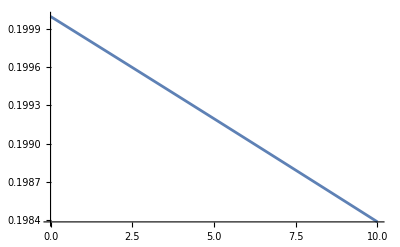

```mathematica
Plot[T[t]/.sol,{t,0,10},PlotRange->Full]
```

```mathematica
Manipulate[Module[{sol,T,Ι},sol=NDSolve[{T'[t]==μ1 T[t] (1-T[t])-γ T[t] Ι[t],Ι'[t]==μ2 Ι[t] (1+α T[t]/(T[t]+T0)-Ι[t]/κ),T[0]==ε,Ι[0]==κ},{T,Ι},{t,0,100}];
Plot[Evaluate[T[t]/. sol],{t,0,100},PlotRange->{0,1},PlotLegends->{"T(t)","Ι(t)"},AxesLabel->{"t","T(t)"},PlotLabel->StringJoin["μ1 = ",ToString[μ1],", μ2 = ",ToString[μ2],", T0 = ",ToString[T0],", α = ",ToString[α],", γ = ",ToString[SetPrecision[γ,1]],", ε = ", ToString[ε],", K = ",ToString[κ]]]],{μ1,0.004,0.012,Appearance->"Labeled"},{μ2,0.004,0.012,Appearance->"Labeled"},{T0,0.25,0.75,Appearance->"Labeled"},{κ,0.5,0.75,Appearance->"Labeled"},{α,0.05,0.15,Appearance->"Labeled"},{γ,0,Dynamic[μ1/κ],Appearance->"Labeled"},{ε,0.01,0.99,Appearance->"Labeled"},Initialization:>(κ=0.5;μ1=0.004;μ2=0.004;
T0=0.5;α=0.05;ε=0.5)]
```

```mathematica
Manipulate[Module[{sol,T,Ι},sol=NDSolve[{T'[t]==μ1 T[t] (1-T[t])-γ T[t] Ι[t],Ι'[t]==μ2 Ι[t] (1+α T[t]/(T[t]+T0)-Ι[t]/κ),T[0]==ε,Ι[0]==κ},{T,Ι},{t,0,100}];
Plot[Evaluate[{T[t],Ι[t]}/. sol],{t,0,100},PlotRange->{0,1},PlotLegends->{"T[t]","Ι(t)"},AxesLabel->{"t","Value"},PlotLabel->StringJoin["μ1 = ",ToString[μ1],", μ2 = ",ToString[μ2],", T0 = ",ToString[T0],", α = ",ToString[α],", γ = ",ToString[γ],", ε = ", ToString[ε],", K = ",ToString[κ]]]],{μ1,0.004,0.012,Appearance->"Labeled"},{μ2,0.004,0.012,Appearance->"Labeled"},{T0,0.25,0.75,Appearance->"Labeled"},{κ,0.5,0.75,Appearance->"Labeled"},{α,0.05,0.15,Appearance->"Labeled"},{γ,0,Dynamic[μ1/κ],Appearance->"Labeled"},{ε,0.01,0.99,Appearance->"Labeled"},Initialization:>(κ=0.5;μ1=0.004;μ2=0.004;
T0=0.5;α=0.05;ε=0.5)]
```

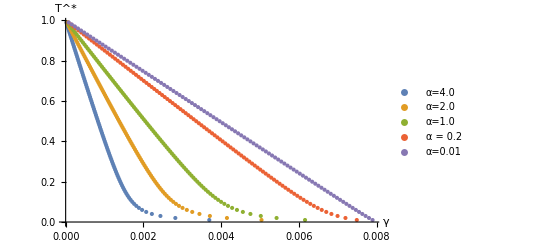

```mathematica
μ1=0.004;
K=0.5;
T0=0.025;
gamma[T_,α_]:=μ1 (1-T)/(Κ (1+α T/(T+T0)))

generatePoints[α_]:=Module[{Tvalues,gammavalues,points},Tvalues=Range[0.01,0.99,0.01];
gammavalues=gamma[#,α]&/@Tvalues;
points=Transpose[{gammavalues,Tvalues}];
points]

points1=generatePoints[2.0];
points2=generatePoints[0.2];
points3=generatePoints[1.0];
points4 = generatePoints[0.01];
points5 = generatePoints[4.0];

ListPlot[{points5,points1,points3,points2,points4},PlotLegends->{"α=4.0","α=2.0","α=1.0","α = 0.2","α=0.01"},AxesLabel->{"γ","T^*"},PlotRange->All]
```

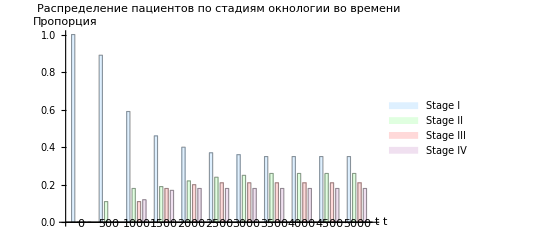

```mathematica
nSimulations=100;
tMax=5000;
timePoints=Range[0,tMax,500]; 
stages={{"Stage I",0,0.25},{"Stage II",0.25,0.5},{"Stage III",0.5,0.75},{"Stage IV",0.75,1}};
stageCounts=ConstantArray[0,{Length[timePoints],Length[stages]}];

Do[μ1=RandomReal[{0.004,0.012}];
μ2=RandomReal[{0.004,0.012}];
α=RandomReal[{0.05,0.15}];
T0=RandomReal[{0.25,0.75}];
K=RandomReal[{0.50,0.75}];
γmax=μ1/K;
γ=RandomReal[{0,γmax}];
sol=NDSolve[{DT'[t]==μ1 DT[t] (1-DT[t])-γ DT[t] DI[t],DI'[t]==μ2 DI[t] (1+α DT[t]/(DT[t]+T0)-DI[t]/K),DT[0]==0.01,DI[0]==K},{DT,DI},{t,0,tMax}];
dtFunc=DT/. First[sol];
Do[tVal=timePoints[[j]];
Tval=dtFunc[tVal];
Which[0<Tval<0.25,stageCounts[[j,1]]++,0.25<=Tval<0.5,stageCounts[[j,2]]++,0.5<=Tval<0.75,stageCounts[[j,3]]++,0.75<=Tval<=1,stageCounts[[j,4]]++],{j,1,Length[timePoints]}],{i,1,nSimulations}];
stageProportions=stageCounts/nSimulations;

BarChart[stageProportions,ChartLegends->stages[[All,1]],ChartLabels->{timePoints,None},AxesLabel->{"t","Пропорция"},FrameTicks->Automatic,PlotLabel->"Распределение пациентов по стадиям окнологии во времени",ChartStyle->{LightBlue,LightGreen,LightRed,LightPurple}]
```

```mathematica
Drug = 0.45;
ϵ = 0.21;
μ1 = 0.004;
μ2 = 0.004;
α = 0.05;
Κ = 0.5;
T0 = 0.25;
γ  =μ1/Κ;
sol = NDSolve[{T'[t] ==μ1 T[t](1-T[t])-γ T[t] *Ι[t] ,
Ι'[t]==μ2 Ι[t](1+α T[t]/(T[t]+T0)-Ι[t]/Κ),T[0] == ϵ,Ι[0]==Κ},{T,Ι},{t,0,1000}]
```

{{T→InterpolatingFunction[…],Ι→InterpolatingFunction[…]}}

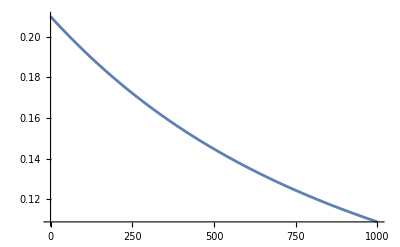

```mathematica
Plot[T[t]/.sol,{t,0,1000}]
```

```mathematica
ClearAll["Global`*"]
```

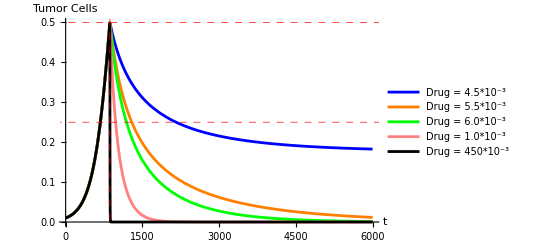

```mathematica
μ1=0.004;
μ2=0.004;
α=0.5;
T0=0.25;
Κ=0.5;
γ=μ1/Κ-0.01; (*gamma<mu1/Kk*)
ϵ = 0.01;
equationsNoDrug={T'[t] == μ1 T[t](1-T[t])-γ T[t] *Ι[t],
Ι'[t]==μ2 Ι[t](1+α T[t]/(T[t]+T0)-Ι[t]/Κ),T[0] == ϵ,Ι[0]==Κ};

solNoDrug=NDSolve[equationsNoDrug,{T,Ι},{t,0,6000}];

tStageIII=t/. FindRoot[T[t]==0.5/. solNoDrug,{t,2000,0,6000}];

drugValues={0.0045,0.0055,0.0060,0.01,0.45};
solutions=Table[NDSolve[{T'[t] == μ1 T[t](1-T[t])-γ T[t] *Ι[t]-drug*T[t],Ι'[t]==μ2 Ι[t](1+α T[t]/(T[t]+T0)-Ι[t]/Κ),T[tStageIII]==(T[tStageIII]/. solNoDrug),Ι[tStageIII]==(Ι[tStageIII]/. solNoDrug)},{T,Ι},{t,tStageIII,6000}],{drug,drugValues}];


combinedT[t_,solDrug_]:=Piecewise[{{T[t]/. solNoDrug,t<=tStageIII},{T[t]/. solDrug[[1]],t>tStageIII}}];

Plot[Evaluate[combinedT[t,#]&/@solutions],{t,0,6000},PlotStyle->{Blue,Orange,Green,Pink,Black},PlotLegends->{"Drug = 4.5*10^-3","Drug = 5.5*10^-3","Drug = 6.0*10^-3","Drug = 1.0*10^-3","Drug = 450*10^-3"},AxesLabel->{"t","Tumor Cells"},PlotRange->All,GridLines->{{tStageIII},{0.25,0.5}},GridLinesStyle->Directive[Red,Dashed,Thick]]
```

-Graphics-

```mathematica
ClearAll[simulateModel];
simulateModel[μ1_,μ2_,α_,T0_,Κ_,γ_,ε_,drugValues_]:=Module[{equationsNoDrug,solNoDrug,tStageIII,solutions,eqns},equationsNoDrug={T'[t]==μ1 T[t] (1-T[t])-γ T[t] Ι[t],Ι'[t]==μ2 Ι[t] (1+α T[t]/(T[t]+T0)-Ι[t]/Κ),T[0]==ε,Ι[0]==Κ};
solNoDrug=NDSolve[equationsNoDrug,{T,Ι},{t,0,6000}];
tStageIII=t/. FindRoot[T[t]==0.5/. solNoDrug,{t,2000,0,6000}];

combinedT[t_,solDrug_]:=Piecewise[{{T[t]/. solNoDrug,t<=tStageIII},{T[t]/. solDrug[[1]],t>tStageIII}}];
solutions=Table[eqns={T'[t]==μ1 T[t] (1-T[t])-γ T[t] Ι[t]-drug T[t],Ι'[t]==μ2 Ι[t] (1+α T[t]/(T[t]+T0)-Ι[t]/Κ),T[tStageIII]==(T[tStageIII]/. solNoDrug),Ι[tStageIII]==(Ι[tStageIII]/. solNoDrug)};
NDSolve[eqns,{T,Ι},{t,tStageIII,6000}],{drug,drugValues}];


Plot[Evaluate[combinedT[t,#]&/@solutions],{t,0,6000},PlotStyle->{Blue,Orange,Green,Pink,Black},PlotLegends->{StringJoin["Drug = ",ToString[#]]&/@drugValues},AxesLabel->{"t","Tumor Cells"},PlotRange->All,GridLines->{{tStageIII},{0.25,0.5}},GridLinesStyle->Directive[Red,Dashed,Thick],PlotLabel->StringJoin["μ1 = ",ToString[SetPrecision[μ1,1 ]],", μ2 = ",ToString[μ2],", T0 = ",ToString[T0],", α = ",ToString[α],", γ = ",ToString[SetPrecision[γ,1]],", ε = ", ToString[ε],", K = ",ToString[Κ]]]];

Manipulate[simulateModel[μ1,μ2,α,T0,Κ,γ,ε,drugValues],{μ1,0.004,0.012},{μ2,0.004,0.012},{α,0.05,0.15},{T0,0.25,0.75},{Κ,0.5,0.75},{γ,0.0001,μ1/Κ-0.001},{ε,0.001,0.1},{drugValues,{{0.0045,0.0055,0.0060,0.01,0.45},{0.1,2,0.02,0.05}}} ]
```